## Band Structure and Propagators

```mathematica
Sx={{0,(√3)/2,0,0},{(√3)/2,0,1,0},{0,1,0,(√3)/2},{0,0,(√3)/2,0}};
Sy={{0,(√3)/(2ⅈ),0,0},{(√3)/(-2ⅈ),0,1/ⅈ,0},{0,-1/ⅈ,0,(√3)/(2ⅈ)},{0,0,(-√3)/(2ⅈ),0}};
Sz={{3/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-3/2}};
MatrixForm[Sx]
MatrixForm[Sy]
MatrixForm[Sz]
```

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

```mathematica
H[kx_,ky_,kz_]:=kx Sx + ky Sy + kz Sz;
MatrixForm[H[kx,ky,kz]]
Eigenvalues[H[kx,ky,kz]]
```

((3 kz)/2 | (√3 kx)/2-1/2 ⅈ √3 ky | 0 | 0
(√3 kx)/2+1/2 ⅈ √3 ky | kz/2 | kx-ⅈ ky | 0
0 | kx+ⅈ ky | -kz/2 | (√3 kx)/2-1/2 ⅈ √3 ky
0 | 0 | (√3 kx)/2+1/2 ⅈ √3 ky | -(3 kz)/2)

{-3/2 √(kx^2+ky^2+kz^2),-1/2 √(kx^2+ky^2+kz^2),1/2 √(kx^2+ky^2+kz^2),3/2 √(kx^2+ky^2+kz^2)}

```mathematica
Plot3D[{-3/2 √(kx^2+ky^2),-1/2 √(kx^2+ky^2),1/2 √(kx^2+ky^2),3/2 √(kx^2+ky^2)},{kx,-1,1},{ky,-1,1},PlotLegends->{"Band 1","Band 2","Band 3","Band 4"}]
```

-Graphics3D-

```mathematica
PropagatorS[ω_,kx_,ky_,kz_]:=Inverse[-ⅈ ω IdentityMatrix[4]+ v H[kx,ky,kz]];
MatrixForm[Factor[PropagatorS[ω,kx,ky,kz]]]
```

((2 (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3+14 ⅈ kx^2 v^2 ω+14 ⅈ ky^2 v^2 ω+2 ⅈ kz^2 v^2 ω+12 kz v ω^2+8 ⅈ ω^3))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(4 √3 (kx-ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(12 (kx-ⅈ ky)^3 v^3)/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
(2 √3 (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 (3 kz v-2 ⅈ ω) (-3 kx^2 v^2-3 ky^2 v^2+3 kz^2 v^2+8 ⅈ kz v ω-4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 (kx-ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 (kx-ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(4 √3 (kx+ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 (kx+ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(2 (3 kz v+2 ⅈ ω) (-3 kx^2 v^2-3 ky^2 v^2+3 kz^2 v^2-8 ⅈ kz v ω-4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(12 (kx+ⅈ ky)^3 v^3)/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 (kx+ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(2 (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3-14 ⅈ kx^2 v^2 ω-14 ⅈ ky^2 v^2 ω-2 ⅈ kz^2 v^2 ω+12 kz v ω^2-8 ⅈ ω^3))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)))

## Self Energy

```mathematica
D[1/((px-kx)^2+(py-ky)^2+(pz-kz)^2),px]/.{px->0,py->0,pz->0}
```

(2 kx)/((kx^2+ky^2+kz^2)^2)

```mathematica
Factor[Simplify[Tr[PropagatorS[ω,kx,ky,kz].Sx]]]
```

(4 kx v (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+20 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))

```mathematica
Integrate[ω^2/((ω^2+1/4 v^2 k^2)(ω^2+9/4 v^2 k^2)),{ω,-Infinity,Infinity},Assumptions->{v,k}∈Reals]
```

π/(2 k v)

```mathematica
Integrate[1/((ω^2+1/4 v^2 k^2)(ω^2+9/4 v^2 k^2)),{ω,-Infinity,Infinity},Assumptions->{v,k}∈Reals]
```

(2 π)/(3 k^3 v^3)

```mathematica
Integrate[Sin[θ]Cos[θ]Cos[θ],{θ,0,π}]
```

2/3

```mathematica
MatrixForm[Factor[Simplify[(2 kx)/((kx^2+ky^2+kz^2)^2) PropagatorS[ω,kx,ky,kz]]]]
```

((4 kx (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3+14 ⅈ kx^2 v^2 ω+14 ⅈ ky^2 v^2 ω+2 ⅈ kz^2 v^2 ω+12 kz v ω^2+8 ⅈ ω^3))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 kx (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(8 √3 kx (kx-ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(24 kx (kx-ⅈ ky)^3 v^3)/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
(4 √3 kx (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(4 kx (3 kz v-2 ⅈ ω) (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (8 kx (kx-ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (8 √3 kx (kx-ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(8 √3 kx (kx+ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (8 kx (kx+ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 kx (3 kz v+2 ⅈ ω) (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 kx (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(24 kx (kx+ⅈ ky)^3 v^3)/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (8 √3 kx (kx+ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 kx (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(4 kx (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3-14 ⅈ kx^2 v^2 ω-14 ⅈ ky^2 v^2 ω-2 ⅈ kz^2 v^2 ω+12 kz v ω^2-8 ⅈ ω^3))/((kx^2+ky^2+kz^2)^2 (kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)))

## Photon Polarization

```mathematica
PolarizationPI[Ω_,qx_,qy_,qz_]:=Tr[PropagatorS[ω+Ω,kx+qx,ky+qy,kz+qz].PropagatorS[ω,kx,ky,kz]];
Factor[Simplify[PolarizationPI[0,0,0,0]]]
```

(16 (45 kx^6 v^6+135 kx^4 ky^2 v^6+135 kx^2 ky^4 v^6+45 ky^6 v^6+135 kx^4 kz^2 v^6+270 kx^2 ky^2 kz^2 v^6+135 ky^4 kz^2 v^6+135 kx^2 kz^4 v^6+135 ky^2 kz^4 v^6+45 kz^6 v^6-92 kx^4 v^4 ω^2-184 kx^2 ky^2 v^4 ω^2-92 ky^4 v^4 ω^2-184 kx^2 kz^2 v^4 ω^2-184 ky^2 kz^2 v^4 ω^2-92 kz^4 v^4 ω^2-80 kx^2 v^2 ω^4-80 ky^2 v^2 ω^4-80 kz^2 v^2 ω^4-64 ω^6))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2)^2 (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)^2)

```mathematica
Integrate[%,{ω,-Infinity,Infinity},Assumptions->{kx,ky,kz,v}∈Reals]
```

ConditionalExpression[0,√(kx^2+ky^2+kz^2) v≠0]

```mathematica
Factor[Simplify[D[PolarizationPI[0,qx,0,0],{qx,2}]/.qx->0]]
```

(32 v^2 (3645 kx^12 v^12+8748 kx^10 ky^2 v^12-10935 kx^8 ky^4 v^12-58320 kx^6 ky^6 v^12-76545 kx^4 ky^8 v^12-43740 kx^2 ky^10 v^12-9477 ky^12 v^12+8748 kx^10 kz^2 v^12-21870 kx^8 ky^2 kz^2 v^12-174960 kx^6 ky^4 kz^2 v^12-306180 kx^4 ky^6 kz^2 v^12-218700 kx^2 ky^8 kz^2 v^12-56862 ky^10 kz^2 v^12-10935 kx^8 kz^4 v^12-174960 kx^6 ky^2 kz^4 v^12-459270 kx^4 ky^4 kz^4 v^12-437400 kx^2 ky^6 kz^4 v^12-142155 ky^8 kz^4 v^12-58320 kx^6 kz^6 v^12-306180 kx^4 ky^2 kz^6 v^12-437400 kx^2 ky^4 kz^6 v^12-189540 ky^6 kz^6 v^12-76545 kx^4 kz^8 v^12-218700 kx^2 ky^2 kz^8 v^12-142155 ky^4 kz^8 v^12-43740 kx^2 kz^10 v^12-56862 ky^2 kz^10 v^12-9477 kz^12 v^12-68040 kx^10 v^10 ω^2-327888 kx^8 ky^2 v^10 ω^2-631152 kx^6 ky^4 v^10 ω^2-606528 kx^4 ky^6 v^10 ω^2-290952 kx^2 ky^8 v^10 ω^2-55728 ky^10 v^10 ω^2-327888 kx^8 kz^2 v^10 ω^2-1262304 kx^6 ky^2 kz^2 v^10 ω^2-1819584 kx^4 ky^4 kz^2 v^10 ω^2-1163808 kx^2 ky^6 kz^2 v^10 ω^2-278640 ky^8 kz^2 v^10 ω^2-631152 kx^6 kz^4 v^10 ω^2-1819584 kx^4 ky^2 kz^4 v^10 ω^2-1745712 kx^2 ky^4 kz^4 v^10 ω^2-557280 ky^6 kz^4 v^10 ω^2-606528 kx^4 kz^6 v^10 ω^2-1163808 kx^2 ky^2 kz^6 v^10 ω^2-557280 ky^4 kz^6 v^10 ω^2-290952 kx^2 kz^8 v^10 ω^2-278640 ky^2 kz^8 v^10 ω^2-55728 kz^10 v^10 ω^2-64080 kx^8 v^8 ω^4-245376 kx^6 ky^2 v^8 ω^4-351648 kx^4 ky^4 v^8 ω^4-223488 kx^2 ky^6 v^8 ω^4-53136 ky^8 v^8 ω^4-245376 kx^6 kz^2 v^8 ω^4-703296 kx^4 ky^2 kz^2 v^8 ω^4-670464 kx^2 ky^4 kz^2 v^8 ω^4-212544 ky^6 kz^2 v^8 ω^4-351648 kx^4 kz^4 v^8 ω^4-670464 kx^2 ky^2 kz^4 v^8 ω^4-318816 ky^4 kz^4 v^8 ω^4-223488 kx^2 kz^6 v^8 ω^4-212544 ky^2 kz^6 v^8 ω^4-53136 kz^8 v^8 ω^4+2304 kx^6 v^6 ω^6+93696 kx^4 ky^2 v^6 ω^6+180480 kx^2 ky^4 v^6 ω^6+89088 ky^6 v^6 ω^6+93696 kx^4 kz^2 v^6 ω^6+360960 kx^2 ky^2 kz^2 v^6 ω^6+267264 ky^4 kz^2 v^6 ω^6+180480 kx^2 kz^4 v^6 ω^6+267264 ky^2 kz^4 v^6 ω^6+89088 kz^6 v^6 ω^6-113920 kx^4 v^4 ω^8-33792 kx^2 ky^2 v^4 ω^8+80128 ky^4 v^4 ω^8-33792 kx^2 kz^2 v^4 ω^8+160256 ky^2 kz^2 v^4 ω^8+80128 kz^4 v^4 ω^8-215040 kx^2 v^2 ω^10+61440 ky^2 v^2 ω^10+61440 kz^2 v^2 ω^10+20480 ω^12))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2)^4 (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)^4)

```mathematica
Integrate[%140,{ω,-Infinity,Infinity},Assumptions->{kx,ky,kz,v}∈Reals]
```

ConditionalExpression[-(8 (ky^2+kz^2) π v^2)/((kx^2+ky^2+kz^2)^(5/2) Abs[v]^3),√(kx^2+ky^2+kz^2) v≠0]

```mathematica
Factor[Simplify[D[PolarizationPI[Ω,0,0,0],{Ω,2}]/.Ω->0]]
```

-((128 (3321 kx^12 v^12+19926 kx^10 ky^2 v^12+49815 kx^8 ky^4 v^12+66420 kx^6 ky^6 v^12+49815 kx^4 ky^8 v^12+19926 kx^2 ky^10 v^12+3321 ky^12 v^12+19926 kx^10 kz^2 v^12+99630 kx^8 ky^2 kz^2 v^12+199260 kx^6 ky^4 kz^2 v^12+199260 kx^4 ky^6 kz^2 v^12+99630 kx^2 ky^8 kz^2 v^12+19926 ky^10 kz^2 v^12+49815 kx^8 kz^4 v^12+199260 kx^6 ky^2 kz^4 v^12+298890 kx^4 ky^4 kz^4 v^12+199260 kx^2 ky^6 kz^4 v^12+49815 ky^8 kz^4 v^12+66420 kx^6 kz^6 v^12+199260 kx^4 ky^2 kz^6 v^12+199260 kx^2 ky^4 kz^6 v^12+66420 ky^6 kz^6 v^12+49815 kx^4 kz^8 v^12+99630 kx^2 ky^2 kz^8 v^12+49815 ky^4 kz^8 v^12+19926 kx^2 kz^10 v^12+19926 ky^2 kz^10 v^12+3321 kz^12 v^12-72360 kx^10 v^10 ω^2-361800 kx^8 ky^2 v^10 ω^2-723600 kx^6 ky^4 v^10 ω^2-723600 kx^4 ky^6 v^10 ω^2-361800 kx^2 ky^8 v^10 ω^2-72360 ky^10 v^10 ω^2-361800 kx^8 kz^2 v^10 ω^2-1447200 kx^6 ky^2 kz^2 v^10 ω^2-2170800 kx^4 ky^4 kz^2 v^10 ω^2-1447200 kx^2 ky^6 kz^2 v^10 ω^2-361800 ky^8 kz^2 v^10 ω^2-723600 kx^6 kz^4 v^10 ω^2-2170800 kx^4 ky^2 kz^4 v^10 ω^2-2170800 kx^2 ky^4 kz^4 v^10 ω^2-723600 ky^6 kz^4 v^10 ω^2-723600 kx^4 kz^6 v^10 ω^2-1447200 kx^2 ky^2 kz^6 v^10 ω^2-723600 ky^4 kz^6 v^10 ω^2-361800 kx^2 kz^8 v^10 ω^2-361800 ky^2 kz^8 v^10 ω^2-72360 kz^10 v^10 ω^2-81424 kx^8 v^8 ω^4-325696 kx^6 ky^2 v^8 ω^4-488544 kx^4 ky^4 v^8 ω^4-325696 kx^2 ky^6 v^8 ω^4-81424 ky^8 v^8 ω^4-325696 kx^6 kz^2 v^8 ω^4-977088 kx^4 ky^2 kz^2 v^8 ω^4-977088 kx^2 ky^4 kz^2 v^8 ω^4-325696 ky^6 kz^2 v^8 ω^4-488544 kx^4 kz^4 v^8 ω^4-977088 kx^2 ky^2 kz^4 v^8 ω^4-488544 ky^4 kz^4 v^8 ω^4-325696 kx^2 kz^6 v^8 ω^4-325696 ky^2 kz^6 v^8 ω^4-81424 kz^8 v^8 ω^4+1280 kx^6 v^6 ω^6+3840 kx^4 ky^2 v^6 ω^6+3840 kx^2 ky^4 v^6 ω^6+1280 ky^6 v^6 ω^6+3840 kx^4 kz^2 v^6 ω^6+7680 kx^2 ky^2 kz^2 v^6 ω^6+3840 ky^4 kz^2 v^6 ω^6+3840 kx^2 kz^4 v^6 ω^6+3840 ky^2 kz^4 v^6 ω^6+1280 kz^6 v^6 ω^6+18176 kx^4 v^4 ω^8+36352 kx^2 ky^2 v^4 ω^8+18176 ky^4 v^4 ω^8+36352 kx^2 kz^2 v^4 ω^8+36352 ky^2 kz^2 v^4 ω^8+18176 kz^4 v^4 ω^8-10240 kx^2 v^2 ω^10-10240 ky^2 v^2 ω^10-10240 kz^2 v^2 ω^10+4096 ω^12))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2)^4 (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)^4))

```mathematica
Integrate[%,{ω,-Infinity,Infinity},Assumptions->{kx,ky,kz,v}∈Reals]
```

ConditionalExpression[0,√(kx^2+ky^2+kz^2) v≠0]

```mathematica
Integrate[Sin[θ]Sin[θ]Sin[θ],{θ,0,π}]
```

4/3

## RG Flow of Parameters

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

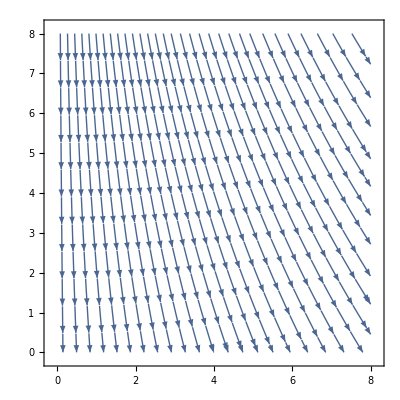

```mathematica
StreamPlot[{4/(75 π^2)g^2,-2/(3 π^2)g^2/v},{v,0,8},{g,0,8}]
```